## DPS equation

```mathematica
mit[d_] := 1/(100/(100+(d/20)))
ehp = FullSimplify[(hp/(66/25)) ((mit[ar]*scale) + (mit[mr]*(1-scale)))]
s = 0.3;
(mit[ar]*scale) /. {hp -> 2000*(66/25), ar -> 2000, mr -> 2000, scale -> s}
Piecewise[{{mit[mr]*(1-scale), scale < 1}}, 0] /. {hp -> 2000*(66/25), ar -> 2000, mr -> 2000, scale -> s}
ehp /. {hp -> 2000*(66/25), ar -> 2000, mr -> 2000, scale -> 0.5}
Clear[hp,ar,mr,scale]
g = Grad[ehp, {hp,ar,mr}]

Manipulate[VectorPlot3D[g /. scale -> ss, {hp, 0, 10000}, {ar, 0, 10000}, {mr, 0, 10000}, VectorPoints -> Coarse, AxesLabel->{hp,ar,mr}], {ss, 0, 1}]
```

(hp (2000+mr+ar scale-mr scale))/5280

0.6

1.4

4000.

{(2000+mr+ar scale-mr scale)/5280,(hp scale)/5280,(hp (1-scale))/5280}

```mathematica
constraints = {scale ≥ 0, scale < 1, hp ≥ 0, ar ≥ 0, mr ≥ 0, hp + ar + mr == 3000};
{knownBestEHP,knownBestDistro} = Assuming[{scale ≥ 0, scale < 1}, FullSimplify[Maximize[{ehp,constraints}, {hp,ar,mr}]]]
```

{Piecewise[{{12500/11, 1/3≤scale≤2/3}, {-(3125 (-5+3 scale)^2)/(66 (-1+scale)), scale<1/3}, {(3125 (2+3 scale)^2)/(66 scale), True}}],{hp→Piecewise[{{3000, 1/3≤scale≤2/3}, {(500 (-5+3 scale))/(-1+scale), 3 scale<1}, {(500 (2+3 scale))/scale, True}}],ar→Piecewise[{{(500 (-2+3 scale))/scale, 3 scale>2}, {0, True}}],mr→Piecewise[{{(500 (-1+3 scale))/(-1+scale), 3 scale<1}, {0, True}}]}}

## Path of steepest ascent

```mathematica
g = Grad[ehp /. {hp -> x, ar -> y, mr -> z}, {x,y,z}]
```

{(2000+scale y+z-scale z)/5280,(scale x)/5280,((1-scale) x)/5280}

```mathematica
{{hp2arUnbounded1,hp2mrUnbounded1}} = {y[x],z[x]} /. DSolve[{
	y'[x] == (g[[1]] /. {y -> y[x], z -> z[x]}) / (g[[2]]), 
	z'[x] == (g[[1]] /. {y -> y[x], z -> z[x]}) / (g[[3]]), 
	y[hp /. knownBestDistro] == (ar /. knownBestDistro), 
	z[hp /. knownBestDistro] == (mr /. knownBestDistro)}, 
	{y[x],z[x]}, x];

hp2arUnbounded = Assuming[scale < 1, FullSimplify[hp2arUnbounded1]]
hp2mrUnbounded = Assuming[scale < 1, FullSimplify[hp2mrUnbounded1]]

hp2arCondition = Assuming[{x >= 0, scale < 1, scale ≥ 0}, FullSimplify@Reduce[{hp2arUnbounded >= 0, scale ≥ 0, scale < 1, x >= 0}]]
hp2mrCondition = Assuming[{x >= 0, scale < 1, scale ≥ 0}, FullSimplify@Reduce[{hp2mrUnbounded >= 0, scale ≥ 0, scale < 1, x >= 0}]]

hp2ar[hp_] := Piecewise[{{hp2arUnbounded, hp2arCondition}} /. x -> hp, 0]
hp2mr[hp_] := Piecewise[{{hp2mrUnbounded, hp2mrCondition}} /. x -> hp, 0]

(*FindInstance[{(hp2mrUnbounded) >= 0, scale ≥ 0, scale < 1, x > 0}, {x,scale}]*)
```

Piecewise[{{(-9000000+x^2)/(9000 scale), 1/3≤scale≤2/3}, {250 (3-5/scale)-((-1+scale)^2 x^2)/(1000 scale (-5+3 scale)), 3 scale<1}, {(750 (-2+scale))/scale+(scale x^2)/(1000 (2+3 scale)), True}}]

Piecewise[{{-(-9000000+x^2)/(9000 (-1+scale)), 1/3≤scale≤2/3}, {(250000 (2+3 scale)^2-scale^2 x^2)/(1000 (-1+scale) (2+3 scale)), 3 scale>2}, {(750 (1+scale))/(-1+scale)+((-1+scale) x^2)/(1000 (-5+3 scale)), True}}]

(x<3000&&750000 (-2+3 scale)+scale x^2≥1000 √3 √(3000000+x^2))||(scale>0&&(x≥3000||(x>2500&&2500+scale (-1500+x)≤x)))

(scale==0&&x==500 √15)||(x>2500&&scale≥1000/(-1500+x))||(x>500 √15&&750000 (-1+3 scale)+scale x^2+1000 √3 √(3000000+x^2)≤x^2)||x≥3000

```mathematica
s = 40/100
{knownBestEHP,knownBestDistro} = Assuming[{scale ≥ 0, scale < 1}, FullSimplify[Maximize[{ehp,{scale ≥ 0, scale < 1, hp ≥ 0, ar ≥ 0, mr ≥ 0, hp + ar + mr == 5000}}, {hp,ar,mr}]]]
N@knownBestDistro /. scale -> s
{knownBestEHP,knownBestDistro} = Assuming[{scale ≥ 0, scale < 1}, FullSimplify[Maximize[{ehp,{scale ≥ 0, scale < 1, hp ≥ 0, ar ≥ 0, mr ≥ 0, hp + ar + mr == 10000}}, {hp,ar,mr}]]]
N@knownBestDistro /. scale -> s
{hp2ar[5000.0] /. scale -> s, hp2mr[5000.] /. scale -> s}
{hp2ar[10000.0] /. scale -> s, hp2mr[10000.] /. scale -> s}
```

2/5

{Piecewise[{{-(3125 (-7+5 scale)^2)/(66 (-1+scale)), scale≤1/2}, {(3125 (2+5 scale)^2)/(66 scale), True}}],{hp→Piecewise[{{(500 (-7+5 scale))/(-1+scale), 2 scale≤1}, {(500 (2+5 scale))/scale, True}}],ar→Piecewise[{{250, 2 scale==1}, {(500 (-2+5 scale))/scale, 2 scale>1}, {0, True}}],mr→Piecewise[{{250, 2 scale==1}, {(500 (-3+5 scale))/(-1+scale), 2 scale<1}, {0, True}}]}}

{hp→4166.67,ar→0.,mr→833.333}

{Piecewise[{{-(6250 (6-5 scale)^2)/(33 (-1+scale)), 10 scale==5+√21||2 scale≤1}, {(6250 (1+5 scale)^2)/(33 scale), True}}],{hp→Piecewise[{{(1000 (-6+5 scale))/(-1+scale), 2 scale≤1}, {1000 (5+1/scale), True}}],ar→Piecewise[{{1500, 2 scale==1}, {1000 (5-1/scale), 2 scale>1}, {0, True}}],mr→Piecewise[{{1500, 2 scale==1}, {1000 (5+1/(-1+scale)), 2 scale<1}, {0, True}}]}}

{hp→6666.67,ar→0.,mr→3333.33}

{4444.44,2962.96}

{25277.8,16851.9}

```mathematica
(*xxx = hp /. knownBestDistro
hmm = f[x] /. DSolve[{
	y'[x] == (g[[1]] /. {y -> y[x], z -> z[x]}) / (g[[2]]), 
	z'[x] == (g[[1]] /. {y -> y[x], z -> z[x]}) / (g[[3]]), 
	f'[x] == x + y'[x] + z'[x],
	f[hp /. knownBestDistro] == (hp /. knownBestDistro) + (ar /. knownBestDistro) + (mr /. knownBestDistro),
	y[hp /. knownBestDistro] == (ar /. knownBestDistro), 
	z[hp /. knownBestDistro] == (mr /. knownBestDistro)}, 
	{y[x],z[x],f[x]}, x]
hmm2 = FullSimplify[hmm]*)
(*
DSolve[{
	Derivative[1,1][y][x,u] == (g[[1]] /. {y -> y[x,u], z -> z[x,u]}) / (g[[2]] /. {y -> y[x,u], z -> z[x,u]}), 
	Derivative[1,1][z][x,u] == (g[[1]] /. {y -> y[x,u], z -> z[x,u]}) / (g[[3]] /. {y -> y[x,u], z -> z[x,u]}), 
	Derivative[1,1][f][x,u] == (g[[1]]) /. {y -> y[x,u], z -> z[x,u]}}, 
	{y[x,u],z[x,u],f[x,u]}, {x,u}] /. scale -> 0.5
*)
(*y[hp /. knownBestDistro, u] == (ar /. knownBestDistro), 
	z[hp /. knownBestDistro, u] == (mr /. knownBestDistro),	
	f[x,20000] == xxx},
	*)
```

```mathematica
(*hmm2 /. {scale -> s, x -> 35000/3}
hmm3 = x /. FullSimplify@Solve[{h == hmm2,h ≥ 0, scale < 1, scale ≥ 0}, x]
hmm4 = Piecewise[hmm3 /. ConditionalExpression[xx_, yy_] :> {xx, yy}]
FullSimplify[hmm4]*)
```

```mathematica
(*s=2/5
gold=5000
constraints = {scale ≥ 0, scale < 1, hp ≥ 0, ar ≥ 0, mr ≥ 0, hp + ar + mr == gold};
{knownBestEHP,knownBestDistro} = Assuming[{scale ≥ 0, scale < 1}, FullSimplify[Maximize[{ehp,constraints}, {hp,ar,mr}]]]

hmm4 /. {h -> 20000, scale -> s}
N@hmm4 /. {h -> 15000, scale -> s}
N@hmm4 /. {h -> 10000, scale -> s}
hmm5 = {hp -> hmm4, ar -> hp2ar[hmm4], mr -> hp2mr[hmm4]} ;

N@knownBestDistro /. scale -> s
hmm5 /. {h -> 20000.0, scale -> s}*)
```

```mathematica
hue[gld_,s_] := {u,hp2ar[u],hp2mr[u]} /. {scale -> s, u -> gld}
s= 0
hue[1000.0,s]
hue[2000.0,s]
hue[5000.0,s]
hue[10000.0,s]
hue[15000.0,s]
hue[30000.0,s]
g
s
Total[hue[30000,s]]
ehp /. {hp -> 15000.0, ar -> 5714, mr -> 12142, scale -> s}
(*
heh[u]:= Module[{constraints}, 
	constraints = {scale ≥ 0, scale < 1, hp ≥ 0, ar ≥ 0, mr ≥ 0, hp + ar + mr == 20000};
	{knownBestEHP,knownBestDistro} = Assuming[{scale ≥ 0, scale < 1}, FullSimplify[Maximize[{ehp,constraints}, {hp,ar,mr}]]]
*)
Show[
	VectorPlot3D[g /. scale -> s, {x,0,30000}, {y,0,30000}, {z,0,30000}, VectorPoints -> Fine, AxesLabel->{hp,ar,mr}, RegionFunction -> Function[{x, y, z}, y ≤ 0]],
	ParametricPlot3D[hue[u,s], {u,0,30000}, AxesLabel->{hp,ar,mr}]
]
```

0

{1000.,0,3545.45}

{2000.,0,3681.82}

{5000.,0,4636.36}

{10000.,0,8045.45}

{15000.,0,13727.3}

{30000.,0,44409.1}

{(2000+scale y+z-scale z)/5280,(scale x)/5280,((1-scale) x)/5280}

0

818500/11

40176.1

-Graphics3D-

```mathematica
gHPodd = x /. Solve[{hp2ar[x] + hp2mr[x] + x == h, h ≥ 0, scale ≥ 0, scale < 1, x ≥ 0}, x, 
					Method -> Reduce]

(*gHPodd = Assuming[{scale ≥ 0, scale < 1, h≥ 0}, FullSimplify[gHPodd]]*)

gHPfixed = Piecewise[gHPodd /. ConditionalExpression[xx_, yy_] :> {xx, yy}]

gHP[gold_] := FullSimplify[gHPfixed /. h -> gold]
gAR[h_] := hp2ar[gHP[h]]
gMR[h_] := hp2mr[gHP[h]]
gDistroDef[h_] := {gHP[h],gAR[h],gMR[h]}
```

{ConditionalExpression[-(1000 (-11+10 scale))/(-1+scale)+20 √5 √((22000+11 h-20000 scale-21 h scale+10 h scale^2)/(-1+scale)^2),0<scale<1/2&&(-3500+5000 scale)/(-1+scale)<h<20000],ConditionalExpression[-(1000 (1+10 scale))/scale+20 √5 √((2000+20000 scale+h scale+10 h scale^2)/scale^2),1/2<scale<1&&-5000+h+1500/scale>0&&h<20000],ConditionalExpression[(1000 (-1-9 scale+10 scale^2))/scale+20 √5 √((2000+18000 scale+h scale-19500 scale^2+9 h scale^2+10000 scale^3-10 h scale^3+50000 scale^4)/scale^2),1/2<scale<1&&h>20000],ConditionalExpression[-(1000 (-11 scale+10 scale^2))/(-1+scale)+20 √5 √((60500-209000 scale+11 h scale+310500 scale^2-21 h scale^2-210000 scale^3+10 h scale^3+50000 scale^4)/(-1+scale)^2),0<scale<1/2&&h>20000]}

Piecewise[{{-(1000 (-11+10 scale))/(-1+scale)+20 √5 √((22000+11 h-20000 scale-21 h scale+10 h scale^2)/(-1+scale)^2), 0<scale<1/2&&(-3500+5000 scale)/(-1+scale)<h<20000}, {-(1000 (1+10 scale))/scale+20 √5 √((2000+20000 scale+h scale+10 h scale^2)/scale^2), 1/2<scale<1&&-5000+h+1500/scale>0&&h<20000}, {(1000 (-1-9 scale+10 scale^2))/scale+20 √5 √((2000+18000 scale+h scale-19500 scale^2+9 h scale^2+10000 scale^3-10 h scale^3+50000 scale^4)/scale^2), 1/2<scale<1&&h>20000}, {-(1000 (-11 scale+10 scale^2))/(-1+scale)+20 √5 √((60500-209000 scale+11 h scale+310500 scale^2-21 h scale^2-210000 scale^3+10 h scale^3+50000 scale^4)/(-1+scale)^2), 0<scale<1/2&&h>20000}, {0, True}}]

```mathematica
s=2/5
gold=5000
constraints = {scale ≥ 0, scale < 1, hp ≥ 0, ar ≥ 0, mr ≥ 0, hp + ar + mr == gold};
{knownBestEHP,knownBestDistro} = Assuming[{scale ≥ 0, scale < 1}, FullSimplify[Maximize[{ehp,constraints}, {hp,ar,mr}]]]

N@knownBestDistro /. scale -> s
r = gDistroDef[gold] /. {scale -> s}
N@Total[r]
N@r
```

2/5

5000

{Piecewise[{{-(3125 (-7+5 scale)^2)/(66 (-1+scale)), scale≤1/2}, {(3125 (2+5 scale)^2)/(66 scale), True}}],{hp→Piecewise[{{(500 (-7+5 scale))/(-1+scale), 2 scale≤1}, {(500 (2+5 scale))/scale, True}}],ar→Piecewise[{{250, 2 scale==1}, {(500 (-2+5 scale))/scale, 2 scale>1}, {0, True}}],mr→Piecewise[{{250, 2 scale==1}, {(500 (-3+5 scale))/(-1+scale), 2 scale<1}, {0, True}}]}}

{hp→4166.67,ar→0.,mr→833.333}

{5000/3 (-7+√70),0,2500+2500/21 (-7+√70)^2}

5000.

{2277.67,0.,2722.33}

```mathematica
gDistroDef[10000] /. {scale -> 7/10}
```

Less::nord: Invalid comparison with 15000\ ⅈ/7 attempted.

Less::nord: Invalid comparison with -25000/3 + 15000\ ⅈ/7 attempted.

General::stop: Further output of Less :: nord will be suppressed during this calculation.

{Piecewise[{{10000, 10000<(15000 ⅈ)/7}, {2000/49 (-135/2+15 √(555/2)), 10000<-25000/3+(15000 ⅈ)/7}, {0, True}}],2500/7,0}

15000

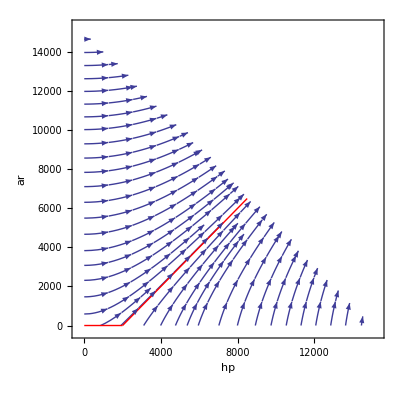

-Graphics3D-

```mathematica
graphLimit = 15000
Block[{scale=0.5},
Show[
  StreamPlot[g, {x, 0, graphLimit}, {y, 0, graphLimit}, 
	RegionFunction -> Function[{x, y, z}, x + y < graphLimit],
	AxesLabel -> {hp,ar}], 

  ParametricPlot[{gHP[u], gAR[u]}, {u, 0, graphLimit}, 
	PlotStyle -> Directive[Red, Thick]]
]]

display[s_] := Block[{scale=s},Show[
	Plot3D[ehp, {hp,0,graphLimit}, {ar,0,graphLimit}, 
	ColorFunction -> Function[{x, y, z},  ColorData["Thermometer"][z]], 
	AxesLabel-> Automatic,
    RegionFunction -> Function[{x, y, z}, x + y < graphLimit]
],

  ParametricPlot3D[{gHP[u], gAR[u], ehp /. {hp -> gHP[u], ar -> gAR[u]}}, {u, 0, graphLimit}, 
	PlotStyle -> Directive[Red, Thickness[0.01]]]
]
]
Show[display[1], display[0.5]]
```

```mathematica
gDistroDef[h]
```

{Piecewise[{{h, 0<h<2000}, {(2000+h)/2, h>2000}, {0, True}}],Max[0,-2000+(Piecewise[{{h, 0<h<2000}, {(2000+h)/2, h>2000}, {0, True}}])]}